```mathematica
{{(*parasite
phenotype/cue 
accuracy*), (*c=T*), (*c=F, Subscript[t, p]<Subscript[t, c]*), (*c=F, Subscript[t, p]>Subscript[t, c]*)}, {(*plastic*), ∫_1^Subscript[t, c] p*Subscript[f, p](t-1)ⅆt+∫_Subscript[t, c]^(Subscript[t, c]+1) Subscript[p, c] Subscript[f, p](t-1)ⅆt+∫_Subscript[t, c+1]^Subscript[t, f] Subscript[p, c] Subscript[f, Subscript[p, c]](t-1)ⅆt, ∫_1^Subscript[t, p] p*Subscript[f, p](t-1)ⅆt+∫_Subscript[t, p]^(Subscript[t, p]+1) Subscript[p, c] Subscript[f, p](t-1)ⅆt+∫_Subscript[t, p+1]^Subscript[t, f] Subscript[p, c] Subscript[f, Subscript[p, c]](t-1)ⅆt, ∫_0^Subscript[t, f] p*Subscript[f, p](t-1)ⅆt}, {(*fixed*), ∫_0^Subscript[t, f] Subscript[p, m]+(1-Subscript[p, m])*βⅆt, ∫_0^Subscript[t, f] Subscript[p, m]+(1-Subscript[p, m])*βⅆt, ∫_0^Subscript[t, f] Subscript[p, m]+(1-Subscript[p, m])*βⅆt}}
```

```mathematica
Subscript[w, p]=r*(∫_1^Subscript[t, c] p*Subscript[f, p](t-1)ⅆt+∫_Subscript[t, c]^(Subscript[t, c]+1) Subscript[p, c] Subscript[f, p](t-1)ⅆt+∫_Subscript[t, c+1]^Subscript[t, f] Subscript[p, c] Subscript[f, Subscript[p, c]](t-1)ⅆt)+
(1-r)*((b)*(∫_1^Subscript[t, p] p*Subscript[f, p](t-1)ⅆt+∫_Subscript[t, p]^(Subscript[t, p]+1) Subscript[p, c] Subscript[f, p](t-1)ⅆt+∫_Subscript[t, p+1]^Subscript[t, f] Subscript[p, c] Subscript[f, Subscript[p, c]](t-1)ⅆt)+
(1-b)*(∫_0^Subscript[t, f] p*Subscript[f, p](t-1)ⅆt));
Subscript[w, f]=∫_0^Subscript[t, f] Subscript[p, m]+(1-Subscript[p, m])*βⅆt;
```

```mathematica
Subscript[f, p][t]=(1-p)*ⅇ^(2*t);
```

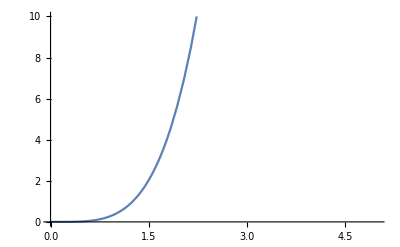

```mathematica
Plot[((1-0.6)),{t, 0,5}, PlotRange->{0,10}]
```

```mathematica
2.87^3
```

23.6399